# Principal Component Analysis

## Finding important directions

We have seen in the lectures how Principal Component Analysis can be used to find the “most important directions” in data. Let’s try it out with a simple 2D dataset that roughly fits on a line:

```mathematica
data=Table[{x,3+2x+RandomVariate[NormalDistribution[0,0.6]]},{x,0,5,0.005}];
```

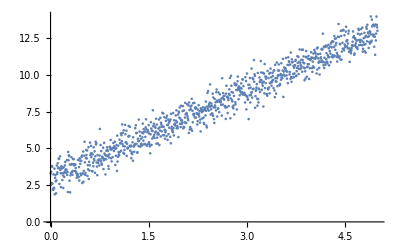

```mathematica
ListPlot[data]
```

In the video lectures we had the matrix of data with rows corresponding to the variables and columns corresponding to the samples (measurements of those variables). Here, we work with the standard convention in statistics and have rows for samples and columns for variables so we will need to keep in mind this different convention.

The first thing we need to do is subtract the mean in each column (i.e. standardize the data):

```mathematica
standardizedData=Standardize[data,Mean,1&];
```

```mathematica
μ=Mean/@Transpose[data]
```

{2.5,7.97241}

```mathematica
σ=StandardDeviation/@Transpose[data]
```

{1.44554,2.97809}

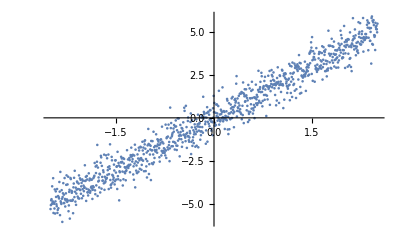

```mathematica
ListPlot[standardizedData]
```

Next we compute the singular value decomposition.

```mathematica
{U,Σ,V}=SingularValueDecomposition[standardizedData];
σs=Diagonal[Σ]
```

{104.353,8.30619}

As expected, we have two singular values, one which is much larger than the other. This reflects the fact that there is much more variance along the line than orthogonal to it.

The singular vectors in the columns of V give us the “most important” directions in the data

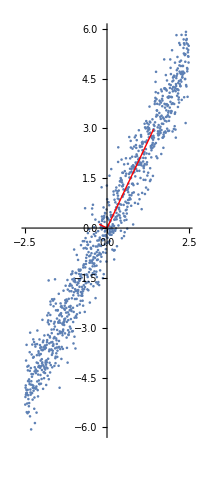

```mathematica
Show[ListPlot[standardizedData,AspectRatio->Automatic],Graphics[{Red,Thick,Line[σs[[1]]/(√(Length[data]-1)){{0,0},-V[[All,1]]}]}],Graphics[{Red,Thick,Line[σs[[2]]/(√(Length[data]-1)){{0,0},V[[All,2]]}]}],PlotRange->All]
```

The singular vectors in the columns of U give us the projection of the data long those “most important” directions (i.e. the same as standardizedData.V)

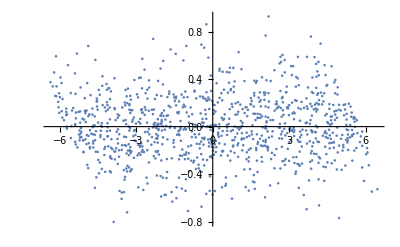

```mathematica
ListPlot[U[[All,1;;2]].Σ[[1;;2,1;;2]]]
```

We can also directly compute this projected form of the data using PrincipalComponents

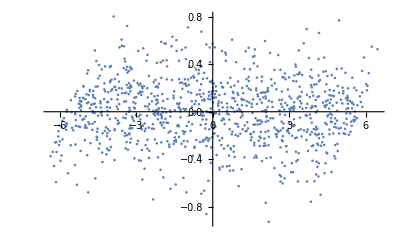

```mathematica
ListPlot[PrincipalComponents[standardizedData]]
```

### In higher dimensions

Construct a 3-dimensional dataset with 3 variables:

```mathematica
data3D=Table[{x,3+2x+RandomVariate[NormalDistribution[0,0.6]],7+4x+RandomVariate[NormalDistribution[0,6]]},{x,0,5,0.005}];
```

```mathematica
ListPointPlot3D[data3D]
```

-Graphics3D-

In this case we choose to standardise by subtracting the mean and dividing by the standard deviation

```mathematica
standardizedData3D=Standardize[data3D];
```

```mathematica
μ=Mean/@Transpose[data3D]
```

{2.5,8.00061,17.2042}

```mathematica
σ=StandardDeviation/@Transpose[data3D]
```

{1.44554,2.94944,8.34602}

```mathematica
ListPointPlot3D[standardizedData3D]
```

-Graphics3D-

Next we compute the singular value decomposition.

```mathematica
{U,Σ,V}=SingularValueDecomposition[standardizedData3D];
σs=Diagonal[Σ];
```

As expected, we have two singular values, one which is much larger than the other. This reflects the fact that there is much more variance along the line than orthogonal to it.

The singular vectors in the columns of V give us the “most important” directions in the data

```mathematica
Show[ListPointPlot3D[standardizedData3D,BoxRatios->Automatic],Graphics3D[{Red,Thick,Line[σs[[1]]/(√(Length[data]-1)){{0,0,0},-V[[All,1]]}]}],Graphics3D[{Red,Thick,Line[σs[[2]]/(√(Length[data]-1)){{0,0,0},V[[All,2]]}]}],Graphics3D[{Red,Thick,Line[σs[[3]]/(√(Length[data]-1)){{0,0,0},V[[All,3]]}]}],PlotRange->All]
```

-Graphics3D-

The singular vectors in the columns of U give us the projection of the data long those “most important” directions (i.e. the same as standardizedData.V)

```mathematica
ListPointPlot3D[U[[All,1;;3]].Σ[[1;;3,1;;3]]]
```

-Graphics3D-

We can also directly compute this projected form of the data using PrincipalComponents

```mathematica
ListPointPlot3D[PrincipalComponents[standardizedData3D]]
```

-Graphics3D-

## Identifying types of flower

Let’s now use PCA to identify the type of a flower based on measurements of their properties. We will work with a dataset for three different types of iris: setosa, versicolor and virginica.

```mathematica
WolframAlpha["Iris",{{"Image:PlantData",1},"Content"}]
```

-Graphics-

The dataset is available directly through Mathematica and contains 4 variables for the length and width of the sepals and petals (in centimeters). Let’s load the data:

```mathematica
iris=ExampleData[{"MachineLearning","FisherIris"}, "Data"];
```

Rearrange the data so that it is grouped by species:

```mathematica
irisbyspecies=GroupBy[iris,Last->First]
```

<|setosa→{{5.1,3.5,1.4,0.2},{4.9,3.,1.4,0.2},{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5.,3.6,1.4,0.2},{5.4,3.9,1.7,0.4},{4.6,3.4,1.4,0.3},{5.,3.4,1.5,0.2},{4.4,2.9,1.4,0.2},{4.9,3.1,1.5,0.1},{5.4,3.7,1.5,0.2},{4.8,3.4,1.6,0.2},{4.8,3.,1.4,0.1},{4.3,3.,1.1,0.1},{5.8,4.,1.2,0.2},{5.7,4.4,1.5,0.4},{5.4,3.9,1.3,0.4},{5.1,3.5,1.4,0.3},{5.7,3.8,1.7,0.3},{5.1,3.8,1.5,0.3},{5.4,3.4,1.7,0.2},{5.1,3.7,1.5,0.4},{4.6,3.6,1.,0.2},{5.1,3.3,1.7,0.5},{4.8,3.4,1.9,0.2},{5.,3.,1.6,0.2},{5.,3.4,1.6,0.4},{5.2,3.5,1.5,0.2},{5.2,3.4,1.4,0.2},{4.7,3.2,1.6,0.2},{4.8,3.1,1.6,0.2},{5.4,3.4,1.5,0.4},{5.2,4.1,1.5,0.1},{5.5,4.2,1.4,0.2},{4.9,3.1,1.5,0.2},{5.,3.2,1.2,0.2},{5.5,3.5,1.3,0.2},{4.9,3.6,1.4,0.1},{4.4,3.,1.3,0.2},{5.1,3.4,1.5,0.2},{5.,3.5,1.3,0.3},{4.5,2.3,1.3,0.3},{4.4,3.2,1.3,0.2},{5.,3.5,1.6,0.6},{5.1,3.8,1.9,0.4},{4.8,3.,1.4,0.3},{5.1,3.8,1.6,0.2},{4.6,3.2,1.4,0.2},{5.3,3.7,1.5,0.2},{5.,3.3,1.4,0.2}},versicolor→{{7.,3.2,4.7,1.4},{6.4,3.2,4.5,1.5},{6.9,3.1,4.9,1.5},{5.5,2.3,4.,1.3},{6.5,2.8,4.6,1.5},{5.7,2.8,4.5,1.3},{6.3,3.3,4.7,1.6},{4.9,2.4,3.3,1.},{6.6,2.9,4.6,1.3},{5.2,2.7,3.9,1.4},{5.,2.,3.5,1.},{5.9,3.,4.2,1.5},{6.,2.2,4.,1.},{6.1,2.9,4.7,1.4},{5.6,2.9,3.6,1.3},{6.7,3.1,4.4,1.4},{5.6,3.,4.5,1.5},{5.8,2.7,4.1,1.},{6.2,2.2,4.5,1.5},{5.6,2.5,3.9,1.1},{5.9,3.2,4.8,1.8},{6.1,2.8,4.,1.3},{6.3,2.5,4.9,1.5},{6.1,2.8,4.7,1.2},{6.4,2.9,4.3,1.3},{6.6,3.,4.4,1.4},{6.8,2.8,4.8,1.4},{6.7,3.,5.,1.7},{6.,2.9,4.5,1.5},{5.7,2.6,3.5,1.},{5.5,2.4,3.8,1.1},{5.5,2.4,3.7,1.},{5.8,2.7,3.9,1.2},{6.,2.7,5.1,1.6},{5.4,3.,4.5,1.5},{6.,3.4,4.5,1.6},{6.7,3.1,4.7,1.5},{6.3,2.3,4.4,1.3},{5.6,3.,4.1,1.3},{5.5,2.5,4.,1.3},{5.5,2.6,4.4,1.2},{6.1,3.,4.6,1.4},{5.8,2.6,4.,1.2},{5.,2.3,3.3,1.},{5.6,2.7,4.2,1.3},{5.7,3.,4.2,1.2},{5.7,2.9,4.2,1.3},{6.2,2.9,4.3,1.3},{5.1,2.5,3.,1.1},{5.7,2.8,4.1,1.3}},virginica→{{6.3,3.3,6.,2.5},{5.8,2.7,5.1,1.9},{7.1,3.,5.9,2.1},{6.3,2.9,5.6,1.8},{6.5,3.,5.8,2.2},{7.6,3.,6.6,2.1},{4.9,2.5,4.5,1.7},{7.3,2.9,6.3,1.8},{6.7,2.5,5.8,1.8},{7.2,3.6,6.1,2.5},{6.5,3.2,5.1,2.},{6.4,2.7,5.3,1.9},{6.8,3.,5.5,2.1},{5.7,2.5,5.,2.},{5.8,2.8,5.1,2.4},{6.4,3.2,5.3,2.3},{6.5,3.,5.5,1.8},{7.7,3.8,6.7,2.2},{7.7,2.6,6.9,2.3},{6.,2.2,5.,1.5},{6.9,3.2,5.7,2.3},{5.6,2.8,4.9,2.},{7.7,2.8,6.7,2.},{6.3,2.7,4.9,1.8},{6.7,3.3,5.7,2.1},{7.2,3.2,6.,1.8},{6.2,2.8,4.8,1.8},{6.1,3.,4.9,1.8},{6.4,2.8,5.6,2.1},{7.2,3.,5.8,1.6},{7.4,2.8,6.1,1.9},{7.9,3.8,6.4,2.},{6.4,2.8,5.6,2.2},{6.3,2.8,5.1,1.5},{6.1,2.6,5.6,1.4},{7.7,3.,6.1,2.3},{6.3,3.4,5.6,2.4},{6.4,3.1,5.5,1.8},{6.,3.,4.8,1.8},{6.9,3.1,5.4,2.1},{6.7,3.1,5.6,2.4},{6.9,3.1,5.1,2.3},{5.8,2.7,5.1,1.9},{6.8,3.2,5.9,2.3},{6.7,3.3,5.7,2.5},{6.7,3.,5.2,2.3},{6.3,2.5,5.,1.9},{6.5,3.,5.2,2.},{6.2,3.4,5.4,2.3},{5.9,3.,5.1,1.8}}|>

Let’s first try to plot the data. This is a 4-dimensional dataset (one dimension for each variable) so we don’t have an easy way to visualise it all. Instead,  just visualise three dimensions by dropping one dimension

```mathematica
ListPointPlot3D[irisbyspecies[[All,All,{2,3,4}]]]
```

-Graphics3D-

It looks like there is hope for separating out the species based on their properties, but it is difficult working with 4-dimensional data. Instead, let’s project it onto the two-dimensional space spanned by the first two principal components. We do this as before: standardize the data, use the SVD to find the principal components and the projection of the data onto those components and then un-standardize the result for plotting.  Instead of doing those steps manually again, let’s use Mathematica’s DimensionReduction function which does exactly that. We tell it to use Principal Component Analysis and to project onto two dimensions

```mathematica
diris=DimensionReduction[iris[[All,1]], 2, Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

The result is a DimensionReducerFunction which takes in a vector of 4 numbers and returns a vector of two numbers obtained by projecting along the two principal directions. We now apply this projection function to our iris data

```mathematica
dirisbyspecies=diris/@irisbyspecies
```

<|setosa→{{2.2647,0.480027},{2.08096,-0.674134},{2.36423,-0.341908},{2.29938,-0.597395},{2.38984,0.646835},{2.07563,1.48918},{2.44403,0.0476442},{2.23285,0.223148},{2.33464,-1.11533},{2.18433,-0.469014},{2.16631,1.04369},{2.32613,0.133078},{2.21845,-0.728676},{2.6331,-0.961507},{2.19874,1.86006},{2.26221,2.68628},{2.20759,1.48361},{2.19035,0.488838},{1.89857,1.40502},{2.34337,1.12785},{1.91432,0.408856},{2.20701,0.924121},{2.77434,0.458344},{1.81867,0.0855585},{2.22716,0.137254},{1.95185,-0.625619},{2.05115,0.242164},{2.16858,0.52715},{2.13956,0.313218},{2.26526,-0.337732},{2.14012,-0.504541},{1.83159,0.423695},{2.61495,1.79358},{2.44618,2.15073},{2.10997,-0.460202},{2.20781,-0.206107},{2.04515,0.661558},{2.52733,0.592293},{2.42963,-0.90418},{2.16971,0.268879},{2.28648,0.441715},{1.85812,-2.33742},{2.55364,-0.479101},{1.96445,0.472327},{2.13706,1.14223},{2.06974,-0.711053},{2.38473,1.12043},{2.39438,-0.386247},{2.22945,0.99796},{2.20383,0.00921636}},versicolor→{{-1.10178,0.862972},{-0.731337,0.594615},{-1.24098,0.616298},{-0.407483,-1.7544},{-1.07547,-0.208421},{-0.388687,-0.593284},{-0.74653,0.773019},{0.487323,-1.85243},{-0.927902,0.0322261},{-0.0114262,-1.03402},{0.110196,-2.65407},{-0.440693,-0.0632952},{-0.562108,-1.76472},{-0.719562,-0.186225},{0.0333547,-0.439003},{-0.875407,0.509064},{-0.350252,-0.196312},{-0.15881,-0.792096},{-1.22509,-1.62224},{-0.164918,-1.30261},{-0.737683,0.396572},{-0.476287,-0.41732},{-1.23418,-0.933326},{-0.632858,-0.416388},{-0.702661,-0.0634118},{-0.874274,0.250793},{-1.25651,-0.077256},{-1.35841,0.331312},{-0.6648,-0.225928},{0.0402586,-1.05872},{-0.130795,-1.56227},{-0.0234527,-1.57248},{-0.241538,-0.777256},{-1.06109,-0.633843},{-0.223979,-0.287774},{-0.429139,0.845582},{-1.04873,0.522052},{-1.04453,-1.38299},{-0.0695883,-0.219503},{-0.283477,-1.32932},{-0.279078,-1.12003},{-0.62457,0.024923},{-0.33653,-0.988404},{0.362183,-2.01924},{-0.288586,-0.85573},{-0.0913607,-0.181192},{-0.227717,-0.38492},{-0.576388,-0.154874},{0.447667,-1.54379},{-0.256731,-0.598852}},virginica→{{-1.84457,0.870421},{-1.15788,-0.69887},{-2.20527,0.56201},{-1.44015,-0.0469876},{-1.86781,0.295045},{-2.75187,0.800409},{-0.367018,-1.5615},{-2.30244,0.420066},{-2.00669,-0.711439},{-2.25978,1.92101},{-1.36418,0.692756},{-1.60268,-0.4217},{-1.8839,0.41925},{-1.26012,-1.16226},{-1.46765,-0.442272},{-1.59008,0.676245},{-1.47143,0.255622},{-2.42633,2.55666},{-3.3107,0.0177809},{-1.26377,-1.70675},{-2.03772,0.910467},{-0.977981,-0.571764},{-2.89765,0.413641},{-1.33323,-0.481811},{-1.70073,1.01392},{-1.95433,1.00778},{-1.1751,-0.316394},{-1.02095,0.064346},{-1.78835,-0.187361},{-1.86365,0.562291},{-2.43595,0.259284},{-2.30493,2.62632},{-1.8627,-0.178549},{-1.11415,-0.292923},{-1.20247,-0.811315},{-2.79877,0.856803},{-1.57626,1.06858},{-1.34629,0.422431},{-0.924825,0.0172231},{-1.85205,0.676128},{-2.01481,0.613886},{-1.90178,0.689575},{-1.15788,-0.69887},{-2.04056,0.867521},{-1.99815,1.04917},{-1.8705,0.386966},{-1.56458,-0.896687},{-1.52117,0.269069},{-1.37279,1.01125},{-0.960656,-0.0243317}}|>

When we plot this lower dimensional representation of the data, we can clearly delineate between the species:

```mathematica
dirisbyspecies
```

<|setosa→{{2.2647,0.480027},{2.08096,-0.674134},{2.36423,-0.341908},{2.29938,-0.597395},{2.38984,0.646835},{2.07563,1.48918},{2.44403,0.0476442},{2.23285,0.223148},{2.33464,-1.11533},{2.18433,-0.469014},{2.16631,1.04369},{2.32613,0.133078},{2.21845,-0.728676},{2.6331,-0.961507},{2.19874,1.86006},{2.26221,2.68628},{2.20759,1.48361},{2.19035,0.488838},{1.89857,1.40502},{2.34337,1.12785},{1.91432,0.408856},{2.20701,0.924121},{2.77434,0.458344},{1.81867,0.0855585},{2.22716,0.137254},{1.95185,-0.625619},{2.05115,0.242164},{2.16858,0.52715},{2.13956,0.313218},{2.26526,-0.337732},{2.14012,-0.504541},{1.83159,0.423695},{2.61495,1.79358},{2.44618,2.15073},{2.10997,-0.460202},{2.20781,-0.206107},{2.04515,0.661558},{2.52733,0.592293},{2.42963,-0.90418},{2.16971,0.268879},{2.28648,0.441715},{1.85812,-2.33742},{2.55364,-0.479101},{1.96445,0.472327},{2.13706,1.14223},{2.06974,-0.711053},{2.38473,1.12043},{2.39438,-0.386247},{2.22945,0.99796},{2.20383,0.00921636}},versicolor→{{-1.10178,0.862972},{-0.731337,0.594615},{-1.24098,0.616298},{-0.407483,-1.7544},{-1.07547,-0.208421},{-0.388687,-0.593284},{-0.74653,0.773019},{0.487323,-1.85243},{-0.927902,0.0322261},{-0.0114262,-1.03402},{0.110196,-2.65407},{-0.440693,-0.0632952},{-0.562108,-1.76472},{-0.719562,-0.186225},{0.0333547,-0.439003},{-0.875407,0.509064},{-0.350252,-0.196312},{-0.15881,-0.792096},{-1.22509,-1.62224},{-0.164918,-1.30261},{-0.737683,0.396572},{-0.476287,-0.41732},{-1.23418,-0.933326},{-0.632858,-0.416388},{-0.702661,-0.0634118},{-0.874274,0.250793},{-1.25651,-0.077256},{-1.35841,0.331312},{-0.6648,-0.225928},{0.0402586,-1.05872},{-0.130795,-1.56227},{-0.0234527,-1.57248},{-0.241538,-0.777256},{-1.06109,-0.633843},{-0.223979,-0.287774},{-0.429139,0.845582},{-1.04873,0.522052},{-1.04453,-1.38299},{-0.0695883,-0.219503},{-0.283477,-1.32932},{-0.279078,-1.12003},{-0.62457,0.024923},{-0.33653,-0.988404},{0.362183,-2.01924},{-0.288586,-0.85573},{-0.0913607,-0.181192},{-0.227717,-0.38492},{-0.576388,-0.154874},{0.447667,-1.54379},{-0.256731,-0.598852}},virginica→{{-1.84457,0.870421},{-1.15788,-0.69887},{-2.20527,0.56201},{-1.44015,-0.0469876},{-1.86781,0.295045},{-2.75187,0.800409},{-0.367018,-1.5615},{-2.30244,0.420066},{-2.00669,-0.711439},{-2.25978,1.92101},{-1.36418,0.692756},{-1.60268,-0.4217},{-1.8839,0.41925},{-1.26012,-1.16226},{-1.46765,-0.442272},{-1.59008,0.676245},{-1.47143,0.255622},{-2.42633,2.55666},{-3.3107,0.0177809},{-1.26377,-1.70675},{-2.03772,0.910467},{-0.977981,-0.571764},{-2.89765,0.413641},{-1.33323,-0.481811},{-1.70073,1.01392},{-1.95433,1.00778},{-1.1751,-0.316394},{-1.02095,0.064346},{-1.78835,-0.187361},{-1.86365,0.562291},{-2.43595,0.259284},{-2.30493,2.62632},{-1.8627,-0.178549},{-1.11415,-0.292923},{-1.20247,-0.811315},{-2.79877,0.856803},{-1.57626,1.06858},{-1.34629,0.422431},{-0.924825,0.0172231},{-1.85205,0.676128},{-2.01481,0.613886},{-1.90178,0.689575},{-1.15788,-0.69887},{-2.04056,0.867521},{-1.99815,1.04917},{-1.8705,0.386966},{-1.56458,-0.896687},{-1.52117,0.269069},{-1.37279,1.01125},{-0.960656,-0.0243317}}|>

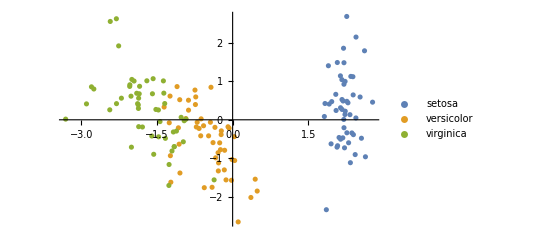

```mathematica
ListPlot[dirisbyspecies]
```

We can go even further than this. We have seen how we can use PCA to project high-dimensional data onto a lower dimensional surface, but we could also reconstruct those projected vectors in the original 4-dimensional space. For example, let’s take one sample of the setosa species:

```mathematica
setosa1=irisbyspecies["setosa"][[1]]
```

{5.1,3.5,1.4,0.2}

We can project this onto the lower-dimensional space:

```mathematica
pcs=diris[setosa1]
```

{2.2647,0.480027}

Then we can take these principal components and combine them with the principal component vectors to reconstruct a 4-vector in the original space. This will be the closest point on our lower-dimensional surface to the original 4-dimensional sample:

```mathematica
diris[pcs,"OriginalData"]
```

{5.01895,3.51485,1.46601,0.251922}

We can do these two steps (projection and reconstruction) in one go by asking for the reconstructed vector directly:

```mathematica
diris[setosa1,"ReconstructedVectors"]
```

{5.01895,3.51485,1.46601,0.251922}

```mathematica
diris[irisbyspecies["setosa"][[1]],"ReconstructedVectors"]
```

```mathematica
{5.018948994974165,3.514854261944867,1.4660128089786664,0.25192198731033677}
```

{5.01895,3.51485,1.46601,0.251922}

Now let’s do this for all sample points and plot the result:

```mathematica
With[{coords={2,3,4}},Row[{Show[ListPointPlot3D[irisbyspecies[[All,All,coords]],ImageSize->500],Graphics3D[{Opacity[0.3],Gray,InfinitePlane[diris[irisbyspecies["setosa"][[1;;3]],"ReconstructedVectors"][[All,coords]]]}]],Show[ListPointPlot3D[(diris[#,"ReconstructedVectors"]&/@irisbyspecies)[[All,All,coords]],ImageSize->500],Graphics3D[{Opacity[0.3],Gray,InfinitePlane[diris[irisbyspecies["setosa"][[1;;3]],"ReconstructedVectors"][[All,coords]]]}]]}]]
```

-Graphics3D--Graphics3D-

Finally, we can also use this approach to fill in missing data. For example, say we had missed a measurement for our first setosa sample

```mathematica
setosa1
```

{5.1,3.5,1.4,0.2}

```mathematica
setosa1missing={5.1,Missing[],1.4,0.2}
```

{5.1,Missing[],1.4,0.2}

We can still project this onto the lower dimensional space

```mathematica
diris[setosa1missing]
```

{2.38754,0.901105}

And we can reconstruct a 4-dimensional vector from this, “filling in” the missing  piece:

```mathematica
diris[setosa1missing,"ReconstructedVectors"]
```

{5.09728,3.69812,1.35872,0.220624}

If all we want to do is fill in the missing piece and leave the others unchanged, then we could do that too:

```mathematica
diris[setosa1missing,"ImputedVectors"]
```

{5.1,3.69812,1.4,0.2}

We won’t cover this idea further in this module, but this is a lot of information about data imputation available online.

## Handwriting recognition

We now look at another example: handwriting recognition, and in particular reading numbers. The National Institute of Standards and Technology in the US have produced a set of 60,000 handwritten numbers collected from Census Bureau employees and high school students. Let’s first load the dataset (this may take a few seconds to download the first time you run it).

```mathematica
ExampleData[{"MachineLearning","MNIST"},"Description"]
```

MNIST Database of handwritten digits.

```mathematica
ExampleData[{"MachineLearning","MNIST"},"VariableDescriptions"]
```

28x28 grayscale image→Integer in the range 1-10

```mathematica
MNIST=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
```

```mathematica
Length[MNIST]
```

60000

This is a list of 60,000 entries, each with an image of a handwritten number and the corresponding integer label (as interpreted by a human). Take a random sample of 30 entries to get an idea of what they look like

```mathematica
RandomSample[MNIST,30]
```

{-Graphics-→1,-Graphics-→0,-Graphics-→8,-Graphics-→7,-Graphics-→1,-Graphics-→2,-Graphics-→5,-Graphics-→8,-Graphics-→3,-Graphics-→6,-Graphics-→8,-Graphics-→6,-Graphics-→7,-Graphics-→2,-Graphics-→6,-Graphics-→9,-Graphics-→6,-Graphics-→2,-Graphics-→5,-Graphics-→7,-Graphics-→6,-Graphics-→8,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→8,-Graphics-→4,-Graphics-→5,-Graphics-→3,-Graphics-→6}

Group the entries by the number they represent

```mathematica
MNISTbynumber=GroupBy[MNIST,Last->First];
```

We will just work with the zeros and ones

```mathematica
MNIST01=Flatten[Values[MNISTbynumber[[1;;2]]]];
MNIST01//Length
```

12665

```mathematica
28 28
```

784

If we think of each 28 x 28 image as a 784 dimensional vector, then we can consider this as a set of 12,665 samples in a 784 dimensional vector space. A random vector in that space won’t look like much, but the 12,665 samples are special as they represent important “directions” in this space.

```mathematica
Row[{Framed[Image[RandomReal[{0,1},{28,28}],ImageSize->Medium]],Framed[Show[MNIST01[[1]],ImageSize->Medium]]}]
```

-Graphics--Graphics-

Let’s see if PCA will allow us to identify the important “directions” corresponding to zeros and ones, and even to differentiate between them. First, let’s convert the images to vectors of numbers:

```mathematica
MNIST01data=Flatten/@ImageData/@MNIST01;
Dimensions[MNIST01data]
```

{12665,784}

Now that we have a matrix, we can use PCA to reduce the 784 dimensional vectors to just the two most important ones

```mathematica
dMNIST01=DimensionReduction[MNIST01data, 2, Method->"PrincipalComponentsAnalysis"];
```

Now we map our dimension reduction projection function over all of the images in our training set

```mathematica
projMNIST01=Map[dMNIST01[Flatten[ImageData[#]]]&,MNISTbynumber[[1;;2]],{2}];
```

If we now visualise all of those samples on our two-dimensional space, we can quite clearly distinguish between zeros and ones:

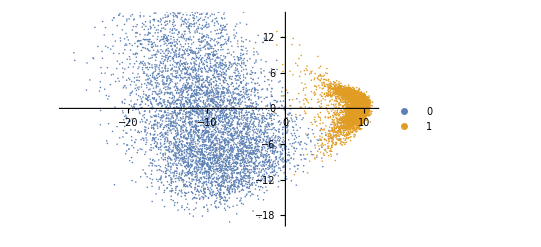

```mathematica
ListPlot[Values[projMNIST01],PlotLegends->Keys[projMNIST01]]
```

That’s all well and good, but it could be that we have just trained our model to understand the images in the training dataset we used. What if we were to throw a new, previously unseen image at it? The MNIST dataset is separated into training and testing datasets for exactly this purpose. Let’s load the test data and see how that fares

```mathematica
MNISTtest=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
MNISTtestbynumber=GroupBy[MNISTtest,Last->First];
```

```mathematica
MNISTtest01=Flatten[Values[MNISTtestbynumber[[1;;2]]]];
MNISTtest01//Length
```

2115

```mathematica
projMNISTtest01=Map[dMNIST01[Flatten[ImageData[#]]]&,MNISTtestbynumber[[1;;2]],{2}];
```

If we now visualise all of those samples on our two-dimensional space, we can quite clearly distinguish between zeros and ones:

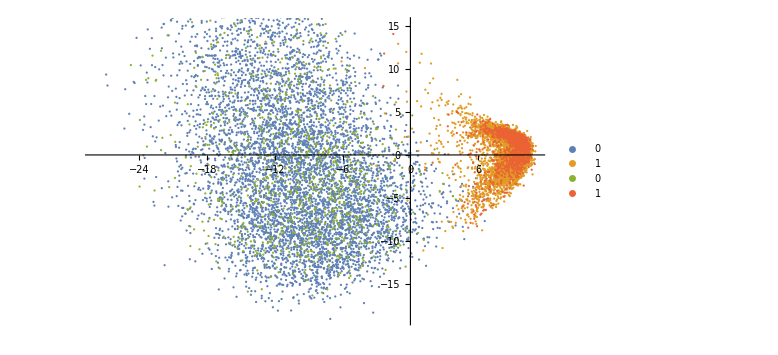

```mathematica
ListPlot[Join[Values[projMNIST01],Values[projMNISTtest01]],PlotLegends->Join[Keys[projMNIST01],Keys[projMNISTtest01]],ImageSize->Large]
```

We can also reconstruct what our model thinks a zero and a one look like:

```mathematica
Row[{Image[Partition[dMNIST01[{-10,0},"OriginalData"],28],ImageSize->Medium],Image[Partition[dMNIST01[{10,0},"OriginalData"],28],ImageSize->Medium]}]
```

-Graphics--Graphics-

And we can even use it to fill in missing data, as we did in the iris case:

```mathematica
vectormissing=MNIST01data[[1]];
vectormissing[[309;;364]]=Missing[];
imagemissing = Image[Partition[Replace[vectormissing, _Missing-> 1,{1}],28],ImageSize->Medium];
imageimputed=Image[Partition[dMNIST01[vectormissing, "ImputedVectors", PerformanceGoal->"Quality"],28],ImageSize->Medium];
```

```mathematica
Row[{Show[MNIST01[[1]],ImageSize->Medium],imagemissing,imageimputed}]
```